```mathematica
file=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"logo.png"}];
logo=Import[file];

Pane[Grid[{{Style["Fitting of Simultaneous-Binding kinetics (kin)","Chapter"],Show[logo,ImageSize->Tiny]},{MouseAppearance[Button[Style["Launch Application (Click me)","Section"],{nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"],SpanFromAbove}},Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Fitting of Simultaneous-Binding kinetics (kin) | -Graphics-
Launch Application (Click me) |

```mathematica
(* Notebook settings*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,GlobalInitializationCellWarning->False]
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],All,EvaluationCell]]
SetOptions[EvaluationNotebook[],InitializationCellEvaluation->True,InitializationCellWarning->False]
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];
(* Load Packges*)	


Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","kinHDComp","kinHDCompStart.m"}]}]];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","buttons.m"}]];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","styles.m"}]];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","inputline.m"}]];


(*Output*)
output="empty";
Off[Export::chtype];
outputinfo="data not yet generated";
kinGenerateOutput[fsteps_]:=
Block[{inputs,datafitted,header,units,column1,column2,column3,signaloutput,put,dataHD,dataD,dataHG,dataG,dataH,specieslegend,dataX},

inputs={{"Quantity","Value","Error"},
{"adjusted R-squared",adjustedrsquared,""},
{"conc(H)",h0in,h0error},
{"conc(D)",d0in,d0error},
{"conc(G)",g0in,g0error},
{"Kequ(HD)",kequhdin,kequhderror},
{"kin(HD)",khd1in,khd1error},
{"kout(HD)",khd1in/kequhdin,khd2error},
{"Kequ(HG)",kequhgin,kequhgerror},
{"kin(HG)",khg1in,khg1error},
{"kout(HG)",khg1in/kequhgin,khg2error},
{"Signal-0",sig0in,sig0error},
{"Signal-HD",sighdin,sighderror},
{"Signal-Dye",sigdin,sigderror},
{"tmax",tmax,"sec"},
{"Date",DateString[],""}
};
header={"time / sec","fitted signal","time / sec","imported data"};

column1=Flatten[inputs[[All,1]]];column2=Flatten[inputs[[All,2]]];column3=Flatten[inputs[[All,3]]];

 dataX=Table[{N[x]},{x,0,tmax,tmax/fsteps}];

 datafitted=Table[modelsignalsim[khd1in,kequhdin,khg1in,kequhgin,sig0in,sighdin,sigdin][x],{x,0,tmax,tmax/fsteps}];

signaloutput=Join[dataX,List/@datafitted,List/@adjusteddata[[All,1]],List/@adjusteddata[[All,2]],2];

put=Join[Prepend[signaloutput,header],List/@column1,List/@column2,List/@column3,2];
Return[put]
];
(*buttons*)
exportbutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Fitting","Save the simulated data as comma delimited .csv"],
Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued",Appearance->None

],"LinkHand"];

datageneratebutton=MouseAppearance[Button[stylesButtonGenericStyle["Generate saveable Data","Generate Datapoints for CSV export"],
output=kinGenerateOutput[N[50]];
outputinfo=output[[16,6]];
,Appearance->None

],"LinkHand"];

filename="fit-temp-kinSBA";

variablessavebutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Parameters","Saves the set values of the parameters"],{
Export[savepath[filename],{h0in,d0in,step,kequhdin,sig0in,sigdin,sighdin,g0in,kequhgin,khd1in, khg1in}]},Appearance->None],"LinkHand"];

variablesloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Saved Parameters","Loads the previously saved values"],{{h0in,d0in,step,kequhdin,sig0in,sigdin,sighdin,g0in,kequhgin,khd1in, khg1in}=Import[savepath[filename]]},Appearance->None],"LinkHand"];
transfersavebutton=MouseAppearance[Button[stylesButtonGenericStyle["Cache for Fit","Saves the set values of the parameters"],{
Export[transferpath[filename],{h0in,d0in,step,kequhdin,sig0in,sigdin,sighdin,g0in,kequhgin,khd1in, khg1in}]},Appearance->None],"LinkHand"];
transferloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Retrieve from Fit","Loads the previously saved values"],
{{h0in,d0in,step,kequhdin,sig0in,sigdin,sighdin,g0in,kequhgin,khd1in, khg1in}=Import[transferpath[filename]]},Appearance->None],"LinkHand"];
(*GUI*)
Clear[h0in,h0error,h0fixed,d0in,d0error,d0fixed,g0in,kequhdin,kequhderror,kequhdfixed,kequhgin,kequhgerror,kequhgfixed,khg1in,khg1error,khg1fixed,khd1in,khd1error,khd1fixed,khd2in,khd2error,khd2fixed,khg2in,khg2error,khg2fixed,tmax,sighdin,sighderror,sighdfixed,sigdin,sigderror,sigdfixed,sig0in,sig0error,sig0fixed,timesteps,concsteps,end,first]

inputline={
{importbutton,variablesloadbutton,variablessavebutton,transfersavebutton,transferloadbutton},
fitilheading,
Flatten[{fitilinputfield["concentration","Host",h0in,h0error,h0fixed,False]}],Flatten[{fitilinfofield["concentration","Host",h0in,h0error,h0fixed,False]}],
Flatten[{fitilinputfield["concentration","Dye",d0in,d0error,d0fixed,False]}],Flatten[{fitilinfofield["concentration","Dye",d0in,d0error,d0fixed,False]}],
Flatten[{fitilinputfield["concentration","Guest",g0in,g0error,g0fixed,False]}],Flatten[{fitilinfofield["concentration","Guest",g0in,g0error,g0fixed,False]}],
Flatten[{fitilinputfield["binding","HD",kequhdin,kequhderror,kequhdfixed,False]}],Flatten[{fitilinfofield["binding","HD",kequhdin,kequhderror,kequhdfixed,False]}],
Flatten[{fitilinputfield["kin","Dye",khd1in,khd1error,khd1fixed,True]}],Flatten[{fitilinfofield["kin","Dye",khd1in,khd1error,khd1fixed,True]}],
Flatten[{fitilinputfield["kout","Dye",khd2in=khd1in/kequhdin,khd2error,khd2fixed,True]}],Flatten[{fitilinfofield["kout","Dye",khd2in,khd2error,khd2fixed,True]}],
Flatten[{fitilinputfield["binding","HG",kequhgin,kequhgerror,kequhgfixed,False]}],Flatten[{fitilinfofield["binding","HG",kequhgin,kequhgerror,kequhgfixed,False]}],
Flatten[{fitilinputfield["kin","Guest",khg1in,khg1error,khg1fixed,True]}],Flatten[{fitilinfofield["kin","Guest",khg1in,khg1error,khg1fixed,True]}],
Flatten[{fitilinputfield["kout","Guest",khg2in=khg1in/kequhgin,khg2error,khg2fixed,True]}],Flatten[{fitilinfofield["kout","Guest",khg2in,khg2error,khg2fixed,True]}],
Flatten[{fitilinputfield["signal","HD",sighdin,sighderror,sighdfixed,True]}],Flatten[{fitilinfofield["signal","HD",sighdin,sighderror,sighdfixed,True]}],
Flatten[{fitilinputfield["signal","D",sigdin,sigderror,sigdfixed,True]}],Flatten[{fitilinfofield["signal","D",sigdin,sigderror,sigdfixed,True]}],
Flatten[{fitilinputfield["signal","0",sig0in,sig0error,sig0fixed,True]}],Flatten[{fitilinfofield["signal","0",sig0in,sig0error,sig0fixed,True]}],
Flatten[{ilinputfield["time","max",tmax],ilinputfield["end","time",end],ilinputfield["start","value",first]}],
Flatten[{ilinfofield["time","max",tmax],ilinfofield["end","time",end],ilinfofield["start","value",first]}]


};


species={1};cfac=1;adjustedrsquared=1;
tmin=0;tmax=2.;end=tmax;timesteps=10;concsteps=22.;stepsize=tmax/100;
h0in=2.21*10^-6;h0error=0;h0fixed=1;
g0in=2.24*10^-6;g0error=0;g0fixed=1;
d0in=2.24*10^-6;d0error=0;d0fixed=1;
khg1in=4000.;khg1error=0;khg1fixed=2;
khd1in=1.9*10^7;khd1error=0;khd1fixed=1;
kequhdin=1.*10^7.38; kequhgerror=0;kequhgfixed=1;
kequhgin=1.*10^7.05;kequhderror=0;kequhdfixed=1;
khd2in=khd1in/kequhdin;khd2error=0;khd2fixed=1;
khg2in=khg1in/kequhgin;khg2error=0;khg2fixed=1;
sighdin=484405.2413662062;sighderror=0;sighdfixed=1;
sigdin=0;sigderror=0;sigdfixed=1;
sig0in=0.3800972433831817;sig0error=0;sig0fixed=1;
step=tmax/timesteps;
factor = 1;
first=0;


f=FileNameJoin[{NotebookDirectory[],"Samples","Sim-kin-SBA.txt"}];
Print[
Style[TableForm[{
{"File format","Time domain","Normalization","Concentration factor","JASCO Import?", "Reset to Minimum?","Trim the data?"},
{"tab delimited .txt file",RadioButtonBar[Dynamic[factor], {1/60. -> "min", 1 -> "sec",1000-> "msec"}],RadioButtonBar[Dynamic[normchoice], {1 -> "None", 2 -> "to N[0,1]",3-> "Devide by max"}],InputField[Dynamic[cfac], FieldSize -> 8],Checkbox[Dynamic[jascoImport]],Checkbox[Dynamic[resetToMin]],Checkbox[Dynamic[trimmer]]}}],"Subsubsection",Black,FontSize->16]
];

Print[Style[TableForm[{{"currently loaded data:",Dynamic[f]},{MouseAppearance[Tooltip[Framed[Style[FileNameSetter[Dynamic[f],"Open",{"Readable files"->{"*.TXT"},"All files"->{"*"}},Appearance->Browse...],"Section",FontSize->18],RoundingRadius->15,Background->LightGray,FrameStyle->Directive[LightGray,12]],"Browse the file"],"LinkHand"]},{}}],
"Subsubsection",Black,FontSize->14
]];
Style[Grid[{{Grid[inputline,Alignment->Left]},{Grid[{{simulationbutton,fitbutton,Dynamic[If[Length[adjusteddata]>0,
datageneratebutton,""]], Dynamic[outputinfo],Dynamic[If[outputinfo=="data not yet generated","",exportbutton]]}}]}
}],"Subsubsection",Black,FontSize->18]
```

File format | Time domain | Normalization | Concentration factor | JASCO Import? | Reset to Minimum? | Trim the data?
tab delimited .txt file |  | min   | sec   | msec |  | None   | to N[0,1]   | Devide by max |  |  |  |

currently loaded data: | 
$CellContext`fOpenAutomaticBrowse...NoneFileNameSetterAutomatic0Automatic | 
 |

Import/Update Data | Load Saved Parameters | Save Parameters | Cache for Fit | Retrieve from Fit |  |  |  | 
Quantitiy | Value | Error | Unit | Fixation |  |  |  | 
[Host]_0 = |  |  | M |  |  |  |  | 
initial Host concentration |  |  | μM |  |  |  |  | 
[Dye]_0 = |  |  | M |  |  |  |  | 
initial Dye concentration |  |  | μM |  |  |  |  | 
[Guest]_0 = |  |  | M |  |  |  |  | 
initial Guest concentration |  |  | μM |  |  |  |  | 
K_equ(HD) = |  |  | M^-1 |  |  |  |  | 
affinity of HD for host |  |  |  |  |  |  |  | 
k_1(Dye) = |  |  | M^-1  s^-1 |  | Fixed   | not fixed |  |  |  | 
Dye ingression rate constant | k_in |  |  |  |  |  |  | 
k_-1(Dye) = |  |  | s^-1 |  | Fixed   | not fixed |  |  |  | 
Dye egression rate constant | k_out |  |  |  |  |  |  | 
K_equ(HG) = |  |  | M^-1 |  |  |  |  | 
affinity of HG for host |  |  |  |  |  |  |  | 
k_1(Guest) = |  |  | M^-1  s^-1 |  | Fixed   | not fixed |  |  |  | 
Guest ingression rate constant | k_in |  |  |  |  |  |  | 
k_-1(Guest) = |  |  | s^-1 |  | Fixed   | not fixed |  |  |  | 
Guest egression rate constant | k_out |  |  |  |  |  |  | 
Signal-HD = |  |  | a.u. |  | Fixed   | not fixed |  |  |  | 
Signal of HD complex |  |  |  |  |  |  |  | 
Signal-D = |  |  | a.u. |  | Fixed   | not fixed |  |  |  | 
Signal of D complex |  |  |  |  |  |  |  | 
Signal-0 = |  |  | a.u. |  | Fixed   | not fixed |  |  |  | 
Signal of 0 complex |  |  |  |  |  |  |  | 
t_max = |  | sec | time_(end point) = |  | number | value_(start point) = |  | number
max time |  | msec | end point = |  | time | start point = |  | value
Simulate | Fit the Data |  |  |

```mathematica
(*Import*)
	dataimport=Import[f,"Table"]; 
	end =  Max[dataimport[[All,1]]];
	step = end/100.;

If[jascoImport, 
i=1;
		dataHeader={};
		While[Not[NumericQ[dataimport[[i,1]]]],dataHeader=AppendTo[dataHeader,dataimport[[i,All]]];
i++;Off[Part::partw]];
		dataXY={};
While[NumericQ[dataimport[[i,1]]],dataXY=AppendTo[dataXY,dataimport[[i,All]]];i++;Off[Part::partw]];
		dataFooter={};While[i≤ First[Dimensions[dataimport]],dataFooter=AppendTo[dataFooter,dataimport[[i,All]]];i++];
		,
		dataXY=dataimport;
	];

If[resetToMin, 
	posMin=First[Flatten[Position[dataXY[[All,2]],Min[dataXY[[All,2]]]]]];
minimizedPart=Length[dataXY]-posMin+1;
	dataXY=Take[dataXY,-minimizedPart];

		,
		dataXY=dataXY;
	];
	
	ymax=Max[dataXY[[All,2]]];
	ymin=Min[dataXY[[All,2]]];
	adjusteddata=dataXY/.{x_,y_}-> {cfac*x/factor,normalize[y,ymax,ymin,normchoice]};
	
	end=Max[adjusteddata[[All,1]]];
first=Min[adjusteddata[[All,2]]];
If[trimmer&&tmax<end, 
closestvalue=Select[adjusteddata[[All,1]],#≥  tmax&,1];
adjusteddata=Take[adjusteddata,Flatten[Position[adjusteddata[[All,1]],closestvalue[[1]]]][[1]]];
];
```

```mathematica
(*equations and functions*)
Clear[h0,d0,g0,hd0,hg0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,kequhg,kequhd,sig];
Clear[h0,d0,g0,hd0,hg0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,kequhg,kequhd,sig];

eqkinsignal={
hd'[t]==-(khd1/kequhd)*hd[t]+khd1*h[t]*d[t],
hg'[t]==-(khg1/kequhg)*hg[t]+khg1*h[t]*g[t],
h'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t]+(khg1/kequhg)*hg[t]-khg1*h[t]*g[t],
d'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t],
g'[t]==(khg1/kequhg)*hg[t]-khg1*h[t]*g[t],
sig[t]==sig0+sighd*hd[t]+sigd*d[t]};






{hd0c,h0c,d0c,hg0c,g0c}=SBAStart[kequhdin,d0in,h0in,kequhgin,g0in];

initialssim={h[0]==h0c,d[0]==d0c,g[0]==g0c,hd[0]==hd0c,hg[0]==hg0c,sig[0]==sig0in+sighdin*hd0c+sigdin*d0c};
modelsignalsim=ParametricNDSolveValue[{eqkinsignal,initialssim},sig,{t,0,tmax},{khd1,kequhd,khg1,kequhg,sig0,sighd,sigd},WorkingPrecision->24];  


Manipulate[
			Show[	
				
				ListPlot[{a2*adjusteddata},PlotStyle-> Blue,PlotRange->All],

				Plot[{a1*modelsignalsim[khd1in,kequhdin,khg1in,kequhgin,sig0in,sighdin,sigdin][x]},{x,0.,tmax},PlotStyle-> {Red,Thick},PlotRange->All],
				
				PlotRange->All,PlotLegends->{"Signal"},ImageSize-> Scaled[0.5],PlotLabel-> Style["Fitting Data","Subsection"],Frame->{{True,False},{True,False}},FrameLabel->{{"Signal / INT",None},{"time / sec",None}},FrameTicks->All
				],
			{{a1,1,Style["Sim Signal",Red]},{1,0}},{{a2,1,Style["Data",Blue]},{1,0}},ControlPlacement->Right
			]
```

```mathematica
Off[ParametricNDSolveValue::ivres];
Off[NonlinearModelFit::sszero];
Off[General::munfl];

Clear[h0,d0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,hd0,hg0,g0,kequhg,kequhd];
{hd0c,h0c,d0c,hg0c,g0c}=SBAStart[kequhdin,d0in,h0in,kequhgin,g0in];
initialsfit={h[0]==h0c,d[0]==d0c,g[0]==g0c,hd[0]==hd0c,hg[0]==hg0c,sig[0]==sig0in+sighdin*hd0c+sigdin*d0c};
modelsignalfit=ParametricNDSolveValue[{eqkinsignal,initialsfit},sig,{t,0,tmax},{khd1,kequhd,khg1,kequhg,sig0,sighd,sigd},WorkingPrecision->24]; 
Clear[h0,d0,g0,hd0,hg0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,kequhg,kequhd,sig];
{hd0c,h0c,d0c,hg0c,g0c}=SBAStart[kequhdin,d0in,h0in,kequhgin,g0in];
vars =  {khd1,kequhd,khg1,kequhg,sig0,sighd,sigd};

initialssim={h[0]==h0in,d[0]==d0in,g[0]==g0in,hd[0]==0.,hg[0]==0., sig[0] == sig0in +sigdin*d0in+sig0in};
modelsignalsim=ParametricNDSolveValue[{eqkinsignal,initialssim},sig,{t,1.*10^-15,tmax},vars];  

inputparameter={};subparameter={};concparameter={};
Clear[h0,d0,khd1,khd2,khg1,khg2,kequhg,kequhd,sig0,sighd,sigd,hd0,hg0,g0];
If[d0fixed== 2,operator=1;AppendTo[inputparameter,{d0,d0in}], (*else*) d0=d0in;];
If[h0fixed== 2,operator=1;AppendTo[inputparameter,{h0,h0in}], (*else*) h0=h0in;];
If[khd1fixed== 2,operator=1;AppendTo[inputparameter,{khd1,khd1in}], (*else*) khd1=khd1in;];
If[khd2fixed== 2,operator=1;AppendTo[inputparameter,{kequhd,kequhdin}], (*else*) kequhd=kequhdin;];
If[khg1fixed== 2,operator=1;AppendTo[inputparameter,{khg1,khg1in}], (*else*) khg1=khg1in;];
If[khg2fixed== 2,operator=1;AppendTo[inputparameter,{kequhg,kequhgin}], (*else*) kequhg=kequhgin;];
If[sighdfixed== 2,operator=1;AppendTo[inputparameter,{sighd,sighdin}], (*else*) sighd=sighdin;];
If[sigdfixed== 2,operator=1;AppendTo[inputparameter,{sigd,sigdin}], (*else*) sigd=sigdin;];
If[sig0fixed== 2,operator=1;AppendTo[inputparameter,{sig0,sig0in}], (*else*) sig0=sig0in;];
nlmfit=NonlinearModelFit[adjusteddata,modelsignalsim[khd1,kequhd,khg1,kequhg,sig0,sighd,sigd][x],inputparameter,x];
bestfit=TableForm[nlmfit["ParameterTableEntries"]];
	(*signal results*)
Clear[sig0out,sighdout,sigdout,khd1out,khd2out,khg1out,khg2out,kequhdout,kequhgout,h0,d0,g0,khd1,khd2,kequhd,khg1,khg2,kequhg,sig0,sighd,sigd]
sig0out=sig0/.nlmfit["BestFitParameters"];sig0pos=Flatten[Position[bestfit[[1,All,1]],sig0out]];
If[NumericQ[sig0out],sig0error=First[bestfit[[1,sig0pos,2]]];sig0in=sig0out;];

sighdout=sighd/.nlmfit["BestFitParameters"];sighdpos=Flatten[Position[bestfit[[1,All,1]],sighdout]];
If[NumericQ[sighdout],sighderror=First[bestfit[[1,sighdpos,2]]];sighdin=sighdout;];

sigdout=sigd/.nlmfit["BestFitParameters"];sigdpos=Flatten[Position[bestfit[[1,All,1]],sigdout]];
If[NumericQ[sigdout],sigderror=First[bestfit[[1,sigdpos,2]]];sigdin=sigdout;];

(*affinity results*)
khd1out=khd1/.nlmfit["BestFitParameters"];khd1pos=Flatten[Position[bestfit[[1,All,1]],khd1out]];
If[NumericQ[khd1out],khd1error=First[bestfit[[1,khd1pos,2]]];khd1in=khd1out;];

khd2out=khd2/.nlmfit["BestFitParameters"];khd2pos=Flatten[Position[bestfit[[1,All,1]],khd2out]];
If[NumericQ[khd2out],khd2error=First[bestfit[[1,khd2pos,2]]];khd2in=khd2out;];
khg1out=khg1/.nlmfit["BestFitParameters"];khg1pos=Flatten[Position[bestfit[[1,All,1]],khg1out]];
If[NumericQ[khg1out],khg1error=First[bestfit[[1,khg1pos,2]]];khg1in=khg1out;];

khg2out=khg2/.nlmfit["BestFitParameters"];khg2pos=Flatten[Position[bestfit[[1,All,1]],khg2out]];
If[NumericQ[khg2out],khg2error=First[bestfit[[1,khg2pos,2]]];khg2in=khg2out;];

kequhdout=kequhd/.nlmfit["BestFitParameters"];kequhdpos=Flatten[Position[bestfit[[1,All,1]],kequhdout]];
If[NumericQ[kequhdout],kequhderror=First[bestfit[[1,kequhdpos,2]]];kequhdin=kequhdout;];

adjustedrsquared  = nlmfit["AdjustedRSquared"];
summary={{"Quantity","Value","Error"},
{"adjusted R-squared",adjustedrsquared,""},
{"conc(H)",h0in,h0error},
{"conc(D)",d0in,d0error},
{"conc(G)",g0in,g0error},
{"Kequ(HD)",kequhdin,kequhderror},
{"k_1(HD)",khd1in,khd1error},
{"k_-1(HD)",khd2in,khd2error},
{"Kequ(HG)",kequhgin,kequhgerror},
{"k_1(HG)",khg1in,khg1error},
{"k_-1(HG)",khg1in/kequhgin,khg2error},
{"Signal-0",sig0in,sig0error},
{"Signal-HD",sighdin,sighderror},
{"Signal-Dye",sigdin,sigderror},

};

Style[TableForm[summary],"Menu"]
```

Quantity | Value | Error
adjusted R-squared | 0.998343 | 
conc(H) | 2.×10^-6 | 0
conc(D) | 4.×10^-6 | 0
conc(G) | 4.×10^-6 | 0
Kequ(HD) | 7.94×10^6 | 0
k_1(HD) | 1.95×10^8 | 0
k_-1(HD) | 0.792052 | 0
Kequ(HG) | 5.01×10^7 | 0
k_1(HG) | 33542.3 | 0.000204494
k_-1(HG) | 0.000669506 | 0
Signal-0 | 0.000547254 | 0
Signal-HD | 540286. | 1.0661×10^-13
Signal-Dye | 1374.63 | 1.52561×10^-10
Null |  |

```mathematica
(*equations and functions*)
Clear[h0,d0,g0,hd0,hg0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,kequhg,kequhd,sig,eqkinsignal];
eqkinsignal={
hd'[t]==-(khd1/kequhd)*hd[t]+khd1*h[t]*d[t],
hg'[t]==-(khg1/kequhg)*hg[t]+khg1*h[t]*g[t],
h'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t]+(khg1/kequhg)*hg[t]-khg1*h[t]*g[t],
d'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t],
g'[t]==(khg1/kequhg)*hg[t]-khg1*h[t]*g[t],
sig[t]==sig0+sighd*hd[t]+sigd*d[t]};

(*equations and functions*)

eqkin={
hd'[t]==-(khd1/kequhd)*hd[t]+khd1*h[t]*d[t],
hg'[t]==-(khg1/kequhg)*hg[t]+khg1*h[t]*g[t],
h'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t]+(khg1/kequhg)*hg[t]-khg1*h[t]*g[t],
d'[t]==(khd1/kequhd)*hd[t]-khd1*h[t]*d[t],
g'[t]==(khg1/kequhg)*hg[t]-khg1*h[t]*g[t]}/.{kequhd-> kequhdin, kequhg -> kequhgin};

Clear[h0,d0,g0,hd0,hg0,khd1,khd2,khg1,khg2,sig0,sighd,sigd,kequhg,kequhd,sig];
{hd0c,h0c,d0c,hg0c,g0c}=SBAStart[kequhdin,d0in,h0in,kequhgin,g0in];
vars =  {khd1,kequhd,khg1,kequhg,sig0,sighd,sigd};

initialssim={h[0]==h0in,d[0]==d0in,g[0]==g0in,hd[0]==0.,hg[0]==0., sig[0] == sig0in +sigdin*d0in+sig0in};
modelsignalsim=ParametricNDSolveValue[{eqkinsignal,initialssim},sig,{t,1.*10^-15,tmax},vars];  

data = Table[{x,modelsignalsim[khd1in,kequhdin,khg1in,kequhgin,sig0in,sighdin,sigdin][x]*RandomReal[{1,0.8}]},{x,0.,tmax,tmax/100}];



(*modelND=NDSolve[{eqkinsignal,initialssim},vars,{t,0,tmax},"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->10}}]*)
```

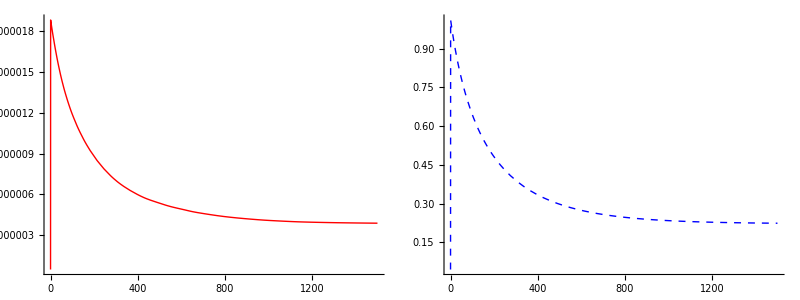

```mathematica
Grid[{{
				Plot[{modelsim[khd1in,khg1in][x]},{x,0.,tmax},PlotStyle-> {Red,Thick},PlotRange->All],
Plot[{modelsignalsim[khd1in,kequhdin,khg1in,kequhgin,sig0in,sighdin,sigdin][x]},{x,0.,tmax},PlotStyle-> {Blue,Thick, Dashed},PlotRange->All]	
												
				}}]
```

```mathematica
inputparameter={};subparameter={};concparameter={};
Clear[h0,d0,khd1,khd2,khg1,khg2,kequhg,kequhd,sig0,sighd,sigd,hd0,hg0,g0];
If[d0fixed== 2,operator=1;AppendTo[inputparameter,{d0,d0in}], (*else*) d0=d0in;];
If[h0fixed== 2,operator=1;AppendTo[inputparameter,{h0,h0in}], (*else*) h0=h0in;];
If[khd1fixed== 2,operator=1;AppendTo[inputparameter,{khd1,khd1in}], (*else*) khd1=khd1in;];
If[khd2fixed== 2,operator=1;AppendTo[inputparameter,{kequhd,kequhdin}], (*else*) kequhd=kequhdin;];
If[khg1fixed== 2,operator=1;AppendTo[inputparameter,{khg1,khg1in}], (*else*) khg1=khg1in;];
If[khg2fixed== 2,operator=1;AppendTo[inputparameter,{kequhg,kequhgin}], (*else*) kequhg=kequhgin;];
If[sighdfixed== 2,operator=1;AppendTo[inputparameter,{sighd,sighdin}], (*else*) sighd=sighdin;];
If[sigdfixed== 2,operator=1;AppendTo[inputparameter,{sigd,sigdin}], (*else*) sigd=sigdin;];
If[sig0fixed== 2,operator=1;AppendTo[inputparameter,{sig0,sig0in}], (*else*) sig0=sig0in;];
nlmfit=NonlinearModelFit[adjusteddata,modelsignalsim[khd1,kequhd,khg1,kequhg,sig0,sighd,sigd][x],inputparameter,x,AccuracyGoal->50];
```

```mathematica
nlmfit["BestFitParameters"]
nlmfit["AdjustedRSquared"]
subparameter
```

{khg1→28747.4}

0.998363

{}